Multiphoton resonance in generalized Rabi model

Module 1: Basic setting
Basis arrangement: (|e,0> |g,0> |e,1> |g,1> ... )

```mathematica
Clear["Global`*"];
nphoton=10; (* Max photon number *)
dim=2*(nphoton+1); (* Dimension of Hilbert space *)
max=10; (* No of eigenvalues wanted *)

σz={{1,0},{0,-1}}; (* Pauli z for atom *)
σx={{0,1},{1,0}}; (* Pauli x for atom *)
σp={{0,1},{0,0}}; (* Raising for atom *)
σm={{0,0},{1,0}}; (* Lowering for atom *)

idenphoton=IdentityMatrix[nphoton+1];
idenatom=IdentityMatrix[2];

(* Annihilation for photon *)
a=Table[0.,nphoton+1,nphoton+1]; 
Do[a[[i,i+1]]=N[Sqrt[i]];,{i,1,nphoton}];

(* Creation for photon *)
adag=Transpose[a];

(* Rabi Hamiltonian *)
H[ωa_,ωc_,g_]:=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,idenatom]+g*KroneckerProduct[a+adag,σx];

(* Jaynes-Cummings Hamiltonian *)
HRWA[ωa_,ωc_,g_]:=ωa/2*KroneckerProduct[idenphoton,σz]+ωc*KroneckerProduct[adag.a,IdentityMatrix[2]]+g*(KroneckerProduct[a,σp]+KroneckerProduct[adag,σm]);
```

Module 2 : Numerical diagonalization

```mathematica
Timing[
ωa=1;
λ=0.06;

Clear[enlist, enRWAlist];

Do[enlist[i]={};,{i,1,max}];
Do[enRWAlist[i]={};,{i,1,max}];

(* Do[veclist[i]={};,{i,1,max}];
Do[vecRWAlist[i]={};,{i,1,max}]; *)

Do[
sol=Eigenvalues[H[ωa,ωc,λ]+100*IdentityMatrix[dim],-max]-100;
solRWA=Eigenvalues[HRWA[ωa,ωc,λ]+100*IdentityMatrix[dim],-max]-100; 

Do[
enlist[i]=Append[enlist[i],{ωc,sol[[max+1-i]]}];
enRWAlist[i]=Append[enRWAlist[i],{ωc,solRWA[[max+1-i]]}]; 

(* veclist[i]=Append[veclist[i]//Chop,{ωc,sol[[2,max+1-i]]}];
vecRWAlist[i]=Append[vecRWAlist[i]//Chop,{ωc,solRWA[[2,max+1-i]]}]; *)

,{i,1,max}];

,{ωc,0.3,0.4,0.0001}];
]
```

{1.22273,Null}

Module 3a : Showing the eigenvalue spectrum

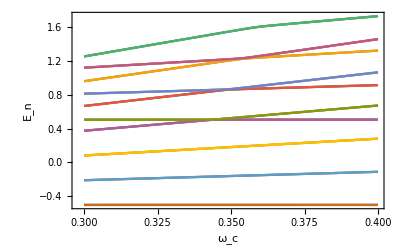

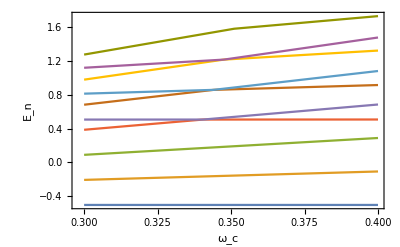

```mathematica
lowest=1;
highest=max;
plotJC={};
Do[
plotRabi=Append[plotRabi,enlist[j]];
plotJC=Append[plotJC,enRWAlist[j]];
,{j,lowest,highest}]

ListPlot[plotRabi,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"ω_c", "E_n"}]
ListPlot[plotJC,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"ω_c","E_n"}]
```

Module 3b : Showing the avoided crossing --- 3-photon resonance

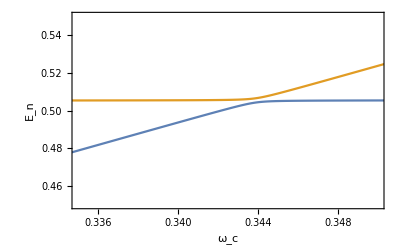

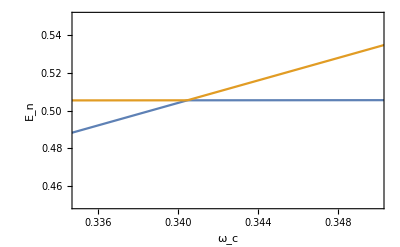

```mathematica
ListPlot[{enlist[4],enlist[5]},PlotRange->{{0.335,0.35},{0.45,0.55}},Joined->True,Frame->True,FrameLabel->{"ω_c", "E_n"}]
ListPlot[{enRWAlist[4],enRWAlist[5]},PlotRange->{{0.335,0.35},{0.45,0.55}},Joined->True,Frame->True,FrameLabel->{"ω_c","E_n"}]
```